## Importing and definitions

```mathematica
Get[NotebookDirectory[]<>"../QMB.wl"]
```

```mathematica
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]]
```

```mathematica
Braket[a_,b_]:=Conjugate[a].b
```

```mathematica
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]]
```

## Global parameters

```mathematica
(*Subscript[h, x]: magnetic field in x direction. L: number of spins*)
{hx,L}={1,11}
(*all interaction parameters Subscript[J, i]=1*)
J=ConstantArray[1,L-1]
```

{1,11}

{1,1,1,1,1,1,1,1,1,1}

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x)

```mathematica
MeanLevelSpacingRatioData={}
```

{}

```mathematica
AbsoluteTiming[
Do[
Module[
{H,eigVals,eigVecs,EvenEigVals},
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
EvenEigVals=eigVals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]]];
AppendTo[MeanLevelSpacingRatioData,{hz,J,MeanLevelSpacingRatio[EvenEigVals]}];
],{hz,1.05,2,0.05},{J,0.05,2,0.05}
]
]
```

{1388.77,Null}

```mathematica
MeanLevelSpacingRatioData
```

{{0.05,0.05,0.435876},{0.05,0.1,0.42656},{0.05,0.15,0.362042},{0.05,0.2,0.375821},{0.05,0.25,0.455823},{0.05,0.3,0.405273},{0.05,0.35,0.364055},{0.05,0.4,0.419863},{0.05,0.45,0.440361},{0.05,0.5,0.429406},{0.05,0.55,0.454035},{0.05,0.6,0.460182},{0.05,0.65,0.450028},{0.05,0.7,0.451331},{0.05,0.75,0.47605},{0.05,0.8,0.482358},{0.05,0.85,0.495696},{0.05,0.9,0.492793},{0.05,0.95,0.473549},{0.05,1.,0.496387},{0.1,0.05,0.445787},{0.1,0.1,0.431166},{0.1,0.15,0.369185},{0.1,0.2,0.379391},{0.1,0.25,0.454541},{0.1,0.3,0.429964},{0.1,0.35,0.412757},{0.1,0.4,0.465966},{0.1,0.45,0.469818},{0.1,0.5,0.480725},{0.1,0.55,0.495919},{0.1,0.6,0.474181},{0.1,0.65,0.51517},{0.1,0.7,0.511238},{0.1,0.75,0.511963},{0.1,0.8,0.512269},{0.1,0.85,0.519702},{0.1,0.9,0.530222},{0.1,0.95,0.524322},{0.1,1.,0.519184},{0.15,0.05,0.426396},{0.15,0.1,0.440687},{0.15,0.15,0.38887},{0.15,0.2,0.40101},{0.15,0.25,0.460405},{0.15,0.3,0.441035},{0.15,0.35,0.398714},{0.15,0.4,0.455154},{0.15,0.45,0.479294},{0.15,0.5,0.509095},{0.15,0.55,0.5105},{0.15,0.6,0.520065},{0.15,0.65,0.532645},{0.15,0.7,0.516232},{0.15,0.75,0.520202},{0.15,0.8,0.525158},{0.15,0.85,0.514419},{0.15,0.9,0.528103},{0.15,0.95,0.518036},{0.15,1.,0.527061},{0.2,0.05,0.413862},{0.2,0.1,0.435086},{0.2,0.15,0.416565},{0.2,0.2,0.429365},{0.2,0.25,0.445838},{0.2,0.3,0.437637},{0.2,0.35,0.440633},{0.2,0.4,0.466343},{0.2,0.45,0.477559},{0.2,0.5,0.506917},{0.2,0.55,0.517934},{0.2,0.6,0.523384},{0.2,0.65,0.528067},{0.2,0.7,0.510163},{0.2,0.75,0.526419},{0.2,0.8,0.505543},{0.2,0.85,0.528354},{0.2,0.9,0.528989},{0.2,0.95,0.528993},{0.2,1.,0.540371},{0.25,0.05,0.405883},{0.25,0.1,0.410737},{0.25,0.15,0.430014},{0.25,0.2,0.447277},{0.25,0.25,0.436149},{0.25,0.3,0.443028},{0.25,0.35,0.45206},{0.25,0.4,0.475582},{0.25,0.45,0.483515},{0.25,0.5,0.500466},{0.25,0.55,0.503766},{0.25,0.6,0.520384},{0.25,0.65,0.525795},{0.25,0.7,0.534939},{0.25,0.75,0.530289},{0.25,0.8,0.523252},{0.25,0.85,0.531532},{0.25,0.9,0.513575},{0.25,0.95,0.516701},{0.25,1.,0.523622},{0.3,0.05,0.40174},{0.3,0.1,0.399325},{0.3,0.15,0.423605},{0.3,0.2,0.442537},{0.3,0.25,0.45184},{0.3,0.3,0.45759},{0.3,0.35,0.474546},{0.3,0.4,0.476599},{0.3,0.45,0.495841},{0.3,0.5,0.5031},{0.3,0.55,0.523868},{0.3,0.6,0.515095},{0.3,0.65,0.522842},{0.3,0.7,0.538521},{0.3,0.75,0.521484},{0.3,0.8,0.533875},{0.3,0.85,0.521921},{0.3,0.9,0.535181},{0.3,0.95,0.521257},{0.3,1.,0.543191},{0.35,0.05,0.412757},{0.35,0.1,0.412145},{0.35,0.15,0.44094},{0.35,0.2,0.462563},{0.35,0.25,0.463282},{0.35,0.3,0.460672},{0.35,0.35,0.468806},{0.35,0.4,0.49525},{0.35,0.45,0.51316},{0.35,0.5,0.504222},{0.35,0.55,0.519663},{0.35,0.6,0.531035},{0.35,0.65,0.536204},{0.35,0.7,0.540222},{0.35,0.75,0.534855},{0.35,0.8,0.535839},{0.35,0.85,0.525874},{0.35,0.9,0.527587},{0.35,0.95,0.546268},{0.35,1.,0.548026},{0.4,0.05,0.399295},{0.4,0.1,0.428379},{0.4,0.15,0.450323},{0.4,0.2,0.461843},{0.4,0.25,0.483975},{0.4,0.3,0.479821},{0.4,0.35,0.496368},{0.4,0.4,0.509193},{0.4,0.45,0.49852},{0.4,0.5,0.516405},{0.4,0.55,0.518647},{0.4,0.6,0.52838},{0.4,0.65,0.537525},{0.4,0.7,0.529173},{0.4,0.75,0.525218},{0.4,0.8,0.526742},{0.4,0.85,0.520002},{0.4,0.9,0.518484},{0.4,0.95,0.534758},{0.4,1.,0.541722},{0.45,0.05,0.403082},{0.45,0.1,0.419196},{0.45,0.15,0.440695},{0.45,0.2,0.460006},{0.45,0.25,0.465765},{0.45,0.3,0.472689},{0.45,0.35,0.502093},{0.45,0.4,0.501631},{0.45,0.45,0.495415},{0.45,0.5,0.521891},{0.45,0.55,0.507535},{0.45,0.6,0.525539},{0.45,0.65,0.551747},{0.45,0.7,0.530502},{0.45,0.75,0.546508},{0.45,0.8,0.529694},{0.45,0.85,0.518161},{0.45,0.9,0.527838},{0.45,0.95,0.522988},{0.45,1.,0.528383},{0.5,0.05,0.392313},{0.5,0.1,0.43143},{0.5,0.15,0.445958},{0.5,0.2,0.464501},{0.5,0.25,0.486684},{0.5,0.3,0.492728},{0.5,0.35,0.492674},{0.5,0.4,0.506533},{0.5,0.45,0.502572},{0.5,0.5,0.502211},{0.5,0.55,0.518218},{0.5,0.6,0.511052},{0.5,0.65,0.520384},{0.5,0.7,0.518807},{0.5,0.75,0.535035},{0.5,0.8,0.53132},{0.5,0.85,0.53804},{0.5,0.9,0.529142},{0.5,0.95,0.536659},{0.5,1.,0.528383},{0.55,0.05,0.421864},{0.55,0.1,0.442052},{0.55,0.15,0.463318},{0.55,0.2,0.475183},{0.55,0.25,0.479392},{0.55,0.3,0.482103},{0.55,0.35,0.487725},{0.55,0.4,0.509243},{0.55,0.45,0.505298},{0.55,0.5,0.51196},{0.55,0.55,0.519048},{0.55,0.6,0.525941},{0.55,0.65,0.515278},{0.55,0.7,0.514015},{0.55,0.75,0.529828},{0.55,0.8,0.535668},{0.55,0.85,0.522687},{0.55,0.9,0.516304},{0.55,0.95,0.523883},{0.55,1.,0.54044},{0.6,0.05,0.405935},{0.6,0.1,0.437013},{0.6,0.15,0.461079},{0.6,0.2,0.480852},{0.6,0.25,0.492364},{0.6,0.3,0.499936},{0.6,0.35,0.51209},{0.6,0.4,0.505292},{0.6,0.45,0.513753},{0.6,0.5,0.514308},{0.6,0.55,0.525639},{0.6,0.6,0.521895},{0.6,0.65,0.496169},{0.6,0.7,0.525387},{0.6,0.75,0.520678},{0.6,0.8,0.520669},{0.6,0.85,0.517135},{0.6,0.9,0.517214},{0.6,0.95,0.546946},{0.6,1.,0.526673},{0.65,0.05,0.430285},{0.65,0.1,0.445402},{0.65,0.15,0.463495},{0.65,0.2,0.470644},{0.65,0.25,0.4763},{0.65,0.3,0.496377},{0.65,0.35,0.512866},{0.65,0.4,0.490805},{0.65,0.45,0.502659},{0.65,0.5,0.541536},{0.65,0.55,0.520196},{0.65,0.6,0.515172},{0.65,0.65,0.535821},{0.65,0.7,0.534493},{0.65,0.75,0.539055},{0.65,0.8,0.539815},{0.65,0.85,0.525466},{0.65,0.9,0.523814},{0.65,0.95,0.517891},{0.65,1.,0.524732},{0.7,0.05,0.420777},{0.7,0.1,0.449167},{0.7,0.15,0.474672},{0.7,0.2,0.474712},{0.7,0.25,0.487561},{0.7,0.3,0.492013},{0.7,0.35,0.488513},{0.7,0.4,0.511888},{0.7,0.45,0.504447},{0.7,0.5,0.525965},{0.7,0.55,0.523252},{0.7,0.6,0.510855},{0.7,0.65,0.523381},{0.7,0.7,0.510966},{0.7,0.75,0.526664},{0.7,0.8,0.524634},{0.7,0.85,0.517035},{0.7,0.9,0.517785},{0.7,0.95,0.515762},{0.7,1.,0.520953},{0.75,0.05,0.410619},{0.75,0.1,0.435919},{0.75,0.15,0.452112},{0.75,0.2,0.466425},{0.75,0.25,0.476187},{0.75,0.3,0.492044},{0.75,0.35,0.514083},{0.75,0.4,0.510175},{0.75,0.45,0.499746},{0.75,0.5,0.503623},{0.75,0.55,0.510205},{0.75,0.6,0.51905},{0.75,0.65,0.507021},{0.75,0.7,0.519683},{0.75,0.75,0.520037},{0.75,0.8,0.520008},{0.75,0.85,0.533746},{0.75,0.9,0.523369},{0.75,0.95,0.52145},{0.75,1.,0.512676},{0.8,0.05,0.40685},{0.8,0.1,0.421348},{0.8,0.15,0.446941},{0.8,0.2,0.455484},{0.8,0.25,0.458628},{0.8,0.3,0.479095},{0.8,0.35,0.479903},{0.8,0.4,0.489121},{0.8,0.45,0.490664},{0.8,0.5,0.514868},{0.8,0.55,0.525626},{0.8,0.6,0.51472},{0.8,0.65,0.523685},{0.8,0.7,0.522641},{0.8,0.75,0.523956},{0.8,0.8,0.53169},{0.8,0.85,0.527327},{0.8,0.9,0.532156},{0.8,0.95,0.517316},{0.8,1.,0.523226},{0.85,0.05,0.399138},{0.85,0.1,0.419894},{0.85,0.15,0.447743},{0.85,0.2,0.449591},{0.85,0.25,0.452964},{0.85,0.3,0.480597},{0.85,0.35,0.482617},{0.85,0.4,0.478754},{0.85,0.45,0.486064},{0.85,0.5,0.50308},{0.85,0.55,0.525583},{0.85,0.6,0.50561},{0.85,0.65,0.518451},{0.85,0.7,0.524545},{0.85,0.75,0.510759},{0.85,0.8,0.529523},{0.85,0.85,0.540163},{0.85,0.9,0.503468},{0.85,0.95,0.531045},{0.85,1.,0.522462},{0.9,0.05,0.419609},{0.9,0.1,0.429557},{0.9,0.15,0.434171},{0.9,0.2,0.433105},{0.9,0.25,0.451945},{0.9,0.3,0.48053},{0.9,0.35,0.493248},{0.9,0.4,0.47833},{0.9,0.45,0.485643},{0.9,0.5,0.490255},{0.9,0.55,0.476059},{0.9,0.6,0.506932},{0.9,0.65,0.525509},{0.9,0.7,0.531903},{0.9,0.75,0.510212},{0.9,0.8,0.512247},{0.9,0.85,0.530914},{0.9,0.9,0.53539},{0.9,0.95,0.528489},{0.9,1.,0.527836},{0.95,0.05,0.40184},{0.95,0.1,0.436029},{0.95,0.15,0.433811},{0.95,0.2,0.448863},{0.95,0.25,0.444669},{0.95,0.3,0.460097},{0.95,0.35,0.481617},{0.95,0.4,0.475859},{0.95,0.45,0.492791},{0.95,0.5,0.497318},{0.95,0.55,0.477478},{0.95,0.6,0.488301},{0.95,0.65,0.500075},{0.95,0.7,0.518648},{0.95,0.75,0.505296},{0.95,0.8,0.520288},{0.95,0.85,0.513582},{0.95,0.9,0.513326},{0.95,0.95,0.520373},{0.95,1.,0.537933},{1.,0.05,0.407455},{1.,0.1,0.429971},{1.,0.15,0.416356},{1.,0.2,0.436887},{1.,0.25,0.448697},{1.,0.3,0.463574},{1.,0.35,0.470681},{1.,0.4,0.468316},{1.,0.45,0.465721},{1.,0.5,0.480922},{1.,0.55,0.485031},{1.,0.6,0.494771},{1.,0.65,0.497214},{1.,0.7,0.491851},{1.,0.75,0.526146},{1.,0.8,0.515504},{1.,0.85,0.520172},{1.,0.9,0.506961},{1.,0.95,0.518369},{1.,1.,0.518369}}

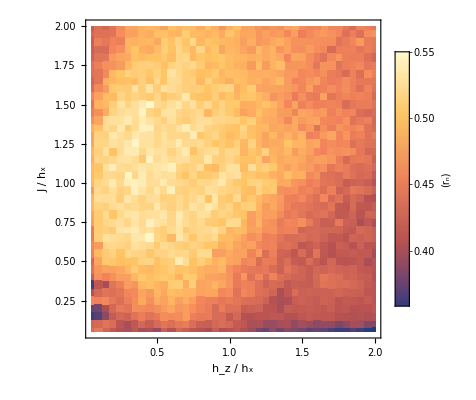

```mathematica
ListDensityPlot[MeanLevelSpacingRatioData,InterpolationOrder->0,
ColorFunction->Automatic,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"(r_n)",LabelStyle->Directive[FontFamily->"Arial",FontSize->20,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->20,Black],
FrameLabel->{"h_z / h_x","J / h_x"}]
```

## Export data and figure

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv",MeanLevelSpacingRatioData,"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png",%516]
```

/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png

```mathematica
data=Import["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv","CSV"];
```

```mathematica
headers1=Quiet[{"# H = \sum_{i=1}^L ( h_x \sigma_i^x h_z \sigma_i^z ) + J \sum_{i=1}^{L-1} \sigma_i^z\sigma_{i+1}^z"}]
headers2={"h_z/h_x","J/h_x","<r_n>"}
```

{# H = \sum_{i=1}^L ( h_x \sigma_i^x h_z \sigma_i^z ) + J \sum_{i=1}^{L-1} \sigma_i^z\sigma_{i+1}^z}

{h_z/h_x,J/h_x,<r_n>}

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv",Prepend[MeanLevelSpacingRatioData,headers2],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv